If[x≥0,x,0]

0.05

0.05

-0.287114+0.428151 If[0.376623-0.0652974 x-1.0797 y≥0,0.376623-0.0652974 x-1.0797 y,0]+0.768442 If[-0.337054-0.375922 x-0.703429 y≥0,-0.337054-0.375922 x-0.703429 y,0]+0.0887475 If[0.0902272+0.461781 x-0.441593 y≥0,0.0902272+0.461781 x-0.441593 y,0]+0.168655 If[0.537572+0.60427 x-0.407068 y≥0,0.537572+0.60427 x-0.407068 y,0]-0.16749 If[-0.113842+0.065978 x-0.220137 y≥0,-0.113842+0.065978 x-0.220137 y,0]-0.310751 If[0.556157-0.376008 x-0.176125 y≥0,0.556157-0.376008 x-0.176125 y,0]-0.457602 If[-0.541698+0.134016 x-0.165132 y≥0,-0.541698+0.134016 x-0.165132 y,0]+0.72504 If[0.196868+0.656153 x-0.153643 y≥0,0.196868+0.656153 x-0.153643 y,0]+0.219899 If[0.316289+0.0587329 x-0.0713105 y≥0,0.316289+0.0587329 x-0.0713105 y,0]+0.187032 If[0.468737-0.0479593 x-0.0404933 y≥0,0.468737-0.0479593 x-0.0404933 y,0]-0.35603 If[0.580727-0.00769053 x+0.00682571 y≥0,0.580727-0.00769053 x+0.00682571 y,0]+0.239811 If[0.483711+0.431783 x+0.0674437 y≥0,0.483711+0.431783 x+0.0674437 y,0]+0.070277 If[0.120105-1.08342 x+0.117578 y≥0,0.120105-1.08342 x+0.117578 y,0]-0.324505 If[-0.410154-0.648293 x+0.170855 y≥0,-0.410154-0.648293 x+0.170855 y,0]-0.792622 If[-0.662699+0.00985506 x+0.640948 y≥0,-0.662699+0.00985506 x+0.640948 y,0]+1.61308 If[-0.175706-1.22072 x+1.20025 y≥0,-0.175706-1.22072 x+1.20025 y,0]

0.031272

0.031272

0.0482491-0.000367545 If[3.08855-0.522321 x-1.0004 y≥0,3.08855-0.522321 x-1.0004 y,0]+2.06475 If[-0.461273+0.150665 x-0.630805 y≥0,-0.461273+0.150665 x-0.630805 y,0]+1.03238 If[0.919955-2.00202 x-0.452864 y≥0,0.919955-2.00202 x-0.452864 y,0]+0.640459 If[0.549966-0.787142 x-0.144241 y≥0,0.549966-0.787142 x-0.144241 y,0]-0.966979 If[0.125311-0.606051 x+0.0788108 y≥0,0.125311-0.606051 x+0.0788108 y,0]-2.23933 If[-0.461197-0.594264 x+0.146048 y≥0,-0.461197-0.594264 x+0.146048 y,0]+0.00242874 If[-0.36866-2.05 x+0.663205 y≥0,-0.36866-2.05 x+0.663205 y,0]-0.0019409 If[-0.613718-3.0431 x+1.00574 y≥0,-0.613718-3.0431 x+1.00574 y,0]

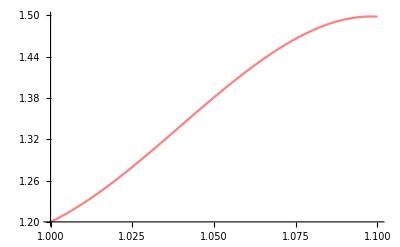

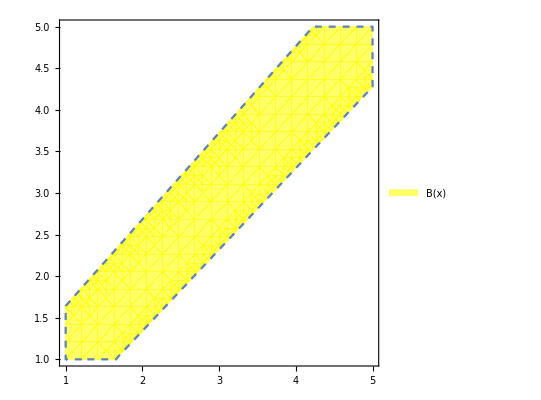

print[g_b]

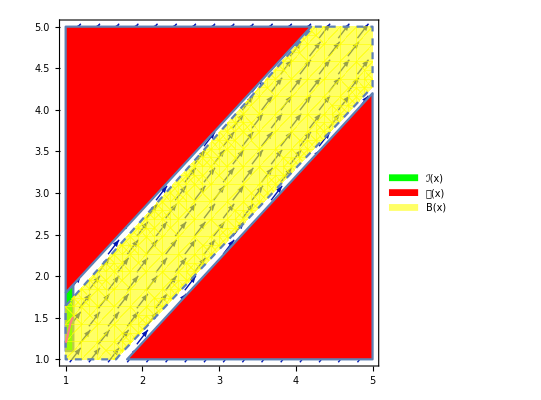

-Graphics-

```mathematica
(*phi=RegionPlot[(x≥0&&x≤0.7&&y≥0.7&&y≤1.5&&y-x<=0.8),{x,0,0.7},{y,0.7,1.5},PlotPoints->50,BoundaryStyle->Directive[RGBColor[0,0.5,0], Thin],PlotStyle->Directive[Blue]]
(*phi ->initial region *)
psi1=RegionPlot[(x≥0&&x≤8&&y≥0&&y≤8&&(y-x)*(y-x)>=1),{x,0,8},{y,0,8},PlotPoints->70,PlotStyle->Directive[Red],BoundaryStyle->Directive[RGBColor[0.5,0,0], Opacity[0.05],Thin]]*)
(* we first give ReLU fuction*)
relu[x_] =If[x>=0,x,0]
(*psi -> unsafe region*)

(*B(x,xˆ)=0.9227x1*x1+0.2348v1*v1+0.9227x2*x2+0.2348v2*v2+0.006x1*v1−0.006x2*v1−0.006x1*v2−0.006x2*v2−0.4696v1*v2−1.845x1x2−0.0002*x2+0.0728,*)
(* this B is only for test*)
(*bc=0.9227*x*x + 0.9227*y*y -1.845*x*y  - 0.0002*y + 0.0728*)
x3 =0.05
x4 =0.05
(*bc = 0.20961230198452*relu[-0.977049978594831*x+0.838193844644194*y+0.673876516960258*x3+0.109865833801004*x4-0.114489667236974]+0.808674414424979*relu[-0.920933153368576*x+1.0062890970721*y-0.176760617228555*x3-0.791901874763677*x4-0.80873469159142]+0.162688373479436*relu[-0.646939421973636*x-0.760381318212942*y-0.666733754645751*x3+1.10370677691161*x4-0.358373162848607]-0.214726527857423*relu[-0.631802584773815*x-1.25178201852823*y-0.428297763637914*x3-0.114215633343116*x4+0.0372529696741055]-0.588395098985064*relu[-0.438681329735811*x-0.297975477898638*y+0.819519236154835*x3+1.53348787259804*x4-0.80622951192207]-0.139058288108177*relu[-0.434578340477944*x-0.475074447140696*y+1.2421679896633*x3+0.0333438417047977*x4-0.231353974340392]-0.183939396623495*relu[-0.424401945870926*x-1.66951018848325*y-0.442102734664958*x3+1.15142783054075*x4-0.0856033743036387]+0.515810270350256*relu[-0.0759138015466691*x+0.0471124902336029*y+0.622074417936798*x3-1.39449843558552*x4+0.651846180792139]+0.210595044988341*relu[-0.0694247105713332*x+0.731764561611308*y-0.503922656752624*x3+0.220967691080613*x4-0.594955377646663]+0.662138647080873*relu[0.0041198681508566*x+0.00135418297968122*y-0.629424928923776*x3-2.18001913904973*x4+0.403642994711347]-0.470780188729511*relu[0.206887832104576*x+0.0570308966072177*y-0.676184169437032*x3+1.50096662080654*x4+0.0362796343748758]-0.838503405113198*relu[0.533126650747215*x-0.54246887065665*y+0.137735538072937*x3-0.976123412853063*x4+0.576685939853719]+0.859452298831454*relu[0.656812512439823*x+0.166080901133304*y-0.254409504485466*x3-1.27516494453622*x4-0.713010049749584]+0.948981746083281*relu[1.00455001805316*x-0.797702269559013*y-0.726660024423718*x3+0.133951257645475*x4+0.479134377762676]-0.0506009606268825*relu[1.04877726296366*x-0.109361246682383*y+0.502806354258896*x3-0.236434097910047*x4+0.091177127429201]-0.51739630585403*relu[1.11125252441803*x-0.650703734377074*y+0.233534388896706*x3-0.528959456589365*x4-1.28212192477566]+0.414080290559346*)
bc =1.61308461895529*relu[-1.22071543012505*x+1.20024505832455*y-0.535718904554417*x3-0.713341946116099*x4-0.113253438015094]+0.070277025378063*relu[-1.08342210950086*x+0.117577698082362*y-0.480653590263889*x3+0.662000841939426*x4+0.111037722166133]-0.324504886440646*relu[-0.648293001529151*x+0.170855036863923*y+0.470775219119227*x3-0.20942257789663*x4-0.423221839273002]-0.310750601320173*relu[-0.376008414391222*x-0.1761245334157*y-0.355048633795721*x3-0.159738933428268*x4+0.581895965779637]+0.768441897697026*relu[-0.375921808029371*x-0.70342923808927*y-1.63080950832886*x3+0.49757607498643*x4-0.280392128988838]+0.428150744013642*relu[-0.0652973880278979*x-1.07969871438646*y-0.802581314688713*x3+0.459281076401297*x4+0.393788346432438]+0.187031916146055*relu[-0.0479593294057424*x-0.0404933006037872*y+0.246028086111993*x3-0.570130108539287*x4+0.48494172655071]-0.35603015743561*relu[-0.00769052785626199*x+0.00682570997803209*y-0.16025919158767*x3+0.413990733378985*x4+0.568040859696521]-0.792621801771999*relu[0.00985505860931576*x+0.640948112702276*y+0.970447989522061*x3-0.209670212793073*x4-0.700738007338096]+0.219898985807527*relu[0.0587328553884066*x-0.0713104715968061*y-0.447198369369384*x3-0.104210679325412*x4+0.34385936433573]-0.167489607208807*relu[0.0659779761510087*x-0.220137174869102*y-0.221283511580529*x3-0.240935621894231*x4-0.0907312585794075]-0.457601673234295*relu[0.134015641255294*x-0.165132195783831*y-0.323872863036866*x3-0.404134116028829*x4-0.505297887660812]+0.239811152365423*relu[0.431783498636469*x+0.0674437000717398*y+0.0850077690790364*x3-0.199612313141617*x4+0.489441455713235]+0.0887475143025102*relu[0.461780852528259*x-0.441592973873257*y-0.46132638579806*x3-0.178494302768587*x4+0.122218193807464]+0.168655126058315*relu[0.604270365078338*x-0.407068218437447*y-0.578060386957278*x3+0.297636411068012*x4+0.55159288641307]+0.725039975323775*relu[0.656153371789636*x-0.153642728734026*y-0.663893516463517*x3-0.657324364888382*x4+0.262928407493188]-0.287113642336253
(*uˆ(x,ˆx,u)=0.8x1−0.8x2+1.5ˆx1−1.5ˆx2+u.*)
(*this is controller*)

(* xuebai *)
initialPlot=RegionPlot[(x≥1&&x≤1.1&&y≥1.1&&y≤2&&y-x<=0.8),{x,1,1.1},{y,1.1,2},PlotStyle->Directive[Green],PlotLegends->SwatchLegend[{"ℐ(x)"}]];
unsafePlot=RegionPlot[(x≥1&&x≤5&&y≥1&&y≤5&&(y-x)*(y-x)>=0.8*0.8),{x,1,5},{y,1,5},PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x)"}]];
bcPlot=RegionPlot[(x≥1&&x≤5&&y≥1&&y≤5&&bc<=1),{x,1,5},{y,1,5},BoundaryStyle->{Dashed},PlotStyle->Directive[Opacity[.6],Yellow],PlotLegends->SwatchLegend[{"B(x)"}]];
u = Random[Real,{0.03,0.05}]
x5 = u
(*uhat = 0.8*x+1.5*y+u*)
(*uhat  = -0.820000366275061*relu[-1.25655286488722*x-1.03813921537532*y+0.380053990335269*x3-0.552455077103081*x4+1.25493600710337*x5-0.112660563425455]-0.716081036328255*relu[-0.543847433985733*x+0.0561651546787756*y-0.2360780966606*x3-0.223898859850695*x4-0.468709844889*x5-0.449735858963336]+0.00879223688096601*relu[-0.523680074455316*x-0.512522647724036*y+0.844342222380732*x3+1.69978278136429*x4+1.36122800893796*x5+0.680799322745128]-0.0108096921452454*relu[-0.467729970730655*x-1.02691968899126*y-0.447488377323604*x3-1.6782702951372*x4-0.0804528021813899*x5+1.18773411395372]-0.00134205109973808*relu[-0.244371174775303*x+0.0312013790843017*y+0.533838850801307*x3+0.677562559847851*x4-0.847794538318824*x5-0.203919719944836]+0.0330705499764603*relu[0.0223543167842997*x-0.255475240540571*y+0.487890723272797*x3-1.09005781756055*x4+1.56616126778349*x5-0.278803403305047]-0.0190013133836391*relu[0.112848302303559*x-1.65411303909963*y-1.98594511828365*x3+1.27084697562287*x4-0.351370538474346*x5+0.173958195637829]+0.0230556355800742*relu[0.153174502593987*x-0.848573693930795*y+1.16246306785423*x3+0.548994077012214*x4+1.17476049203854*x5-0.961747901244111]+0.0455006565279379*)
uhat = -0.00194089918525801*relu[-3.04310205931842*x+1.00574033180266*y+1.48929969166533*x3-1.34791723946631*x4+1.65710140197568*x5-0.672608163239276]+0.00242874247579905*relu[-2.05000400150441*x+0.6632051680725*y-0.523864914734914*x3-0.0525854828290688*x4+1.12244996286789*x5-0.374939265060864]+1.03238116218058*relu[-2.00202072834275*x-0.452864191776889*y+0.301301618883869*x3+0.55736388783268*x4+0.443794096770803*x5+0.86314384243385]+0.64045876776299*relu[-0.787142411235495*x-0.144241152759122*y-0.143113695584753*x3-0.146631258696995*x4+0.280574468825913*x5+0.555679264493473]-0.966978581321368*relu[-0.606051349512228*x+0.0788108348349424*y+0.212837401213284*x3-1.52903228123965*x4-0.822875666199395*x5+0.216853398089884]-2.23933056598771*relu[-0.594264046039552*x+0.146047764739396*y+0.447894370805756*x3+0.442953660540369*x4-0.0694214285593614*x5-0.503568048151583]-0.00036754482974955*relu[-0.522320683056415*x-1.0004025512413*y+1.14463232986057*x3+1.82866127694179*x4+1.30055805975999*x5+2.89921075313481]+2.0647499465471*relu[0.150664864315063*x-0.630805453534331*y+0.309031855344938*x3+1.45921063034412*x4-0.839762775738244*x5-0.523423810326477]+0.0482491116245389
flowPlot=VectorPlot[{x3+u,x4+uhat},{x,1,5},{y,1,5},VectorStyle->{Arrowheads[0.03],Blue}];
inpolt = Plot[{-396.83*x*x*x +1237.30*x*x -1281.84 * x + 442.57},{x,1,1.1},PlotStyle->Directive[Pink]]
(*Vector=StreamPlot[{0.1+0.5*u, 0.1+0.5*uhat},{x,0,8},{y,0,8},StreamScale->0.16,StreamStyle->Gray]*)

(*domain1 = ContourPlot[V==0.048,{x,0,0.7},{y,0.7,1.5},ContourStyle->Directive[Black]]
domain3= ContourPlot[V==0.048,{x,0,8},{y,0,8},ContourStyle->Directive[blue]]*)
g_b = Show[bcPlot]
print[g_b]

graphics=Show[flowPlot,initialPlot,unsafePlot,bcPlot,inpolt ]
Print[graphics];
```

```mathematica
|
```